```mathematica
$ImportFormats;
scatterdata=Import["C:\\Users\\shahn\\OneDrive\\Desktop\\Undergraduate project\\Ge Gm.csv"];
```

```mathematica
qvalues = scatterdata[[2;;12,1]];
```

```mathematica
(*Calculation for Subscript[μ, p] Subscript[G, E]/Subscript[G, M] graph*)
GeGmvalues = scatterdata[[2;;12,13]];
errors1= scatterdata[[2;;12,14]];
GeGmerror=  Table[Around[GeGmvalues[[i]],errors1[[i]]],{i,1,Length[GeGmvalues]}];
RatioGeGmerror= Transpose[{qvalues, GeGmerror}];
RatioGeGm = Transpose[{qvalues, GeGmvalues}];
```

```mathematica
(*fit function for Subscript[μ, p] Subscript[G, E]/Subscript[G, M] graph*)
fitGeGm=  Fit[RatioGeGm,{1,x,x^2,x^3},x];
```

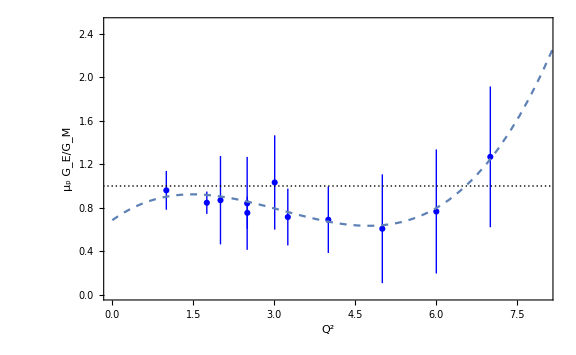

```mathematica
(*Graph for Subscript[μ, p] Subscript[G, E]/Subscript[G, M] vs Q^2*)
Show[ListPlot[RatioGeGmerror,PlotMarkers->Automatic,PlotStyle->Blue,PlotTheme-> "Monochrome"]/.RGBColor[__]:> RGBColor[0,0,1],Plot[fitGeGm,{x,0,10},PlotStyle->Dashed] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"Q^2", "μ_p G_E/G_M"},PlotRange-> {{0,8},{0,2.5}}, GridLines-> {{},{1}}, ImageSize-> Large]
```

```mathematica
(*The Q^2 value and Subscript[μ, p] Subscript[G, E]/Subscript[G, M] valus Of Andivahis et al. are calculated*)
AndivQ= {1.75,2.50,3.25,4.00,5,6,7};
AndivGeGm= {Around[0.910,{ 0.061,0.059}],Around[0.824,{0.072, 0.068}],Around[0.846,{0.124, 0.112}],Around[0.891,{0.138, 0.123}],Around[0.931,{0.192, 0.162}],Around[0.965,{0.241, 0.2}],Around[1.51,{0.275, 0.247}]};
```

```mathematica
(*The Q^2 value and Subscript[μ, p] Subscript[G, E]/Subscript[G, M] valus Of Walker et al. are calculated*)
WalkQ= {1,2.003,2.497,3.007};
WalkGeGd= {Around[1.001,0.072],Around[1.173,0.077],Around[1.101,0.103],Around[1.231,0.141]};
WalkGmGd= {Around[1.017,0.027],Around[1.014,0.077],Around[1.030,0.016],Around[1.012,0.020]};
WalkGeGm = WalkGeGd/WalkGmGd;
```

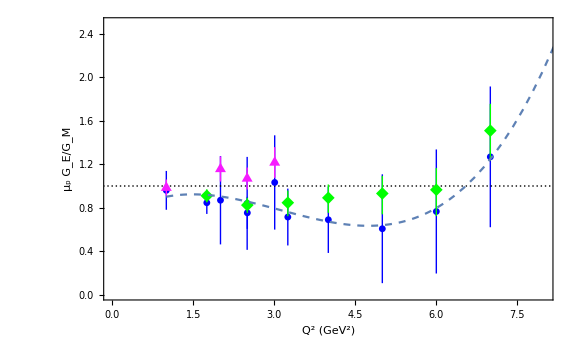

```mathematica
Show[ListPlot[RatioGeGmerror,PlotMarkers->{Automatic,Small} , PlotStyle->Blue,PlotTheme-> "Monochrome"]/.RGBColor[__]:> RGBColor[0,0,1],ListPlot[Transpose[{AndivQ,AndivGeGm}],PlotMarkers->{"◆",Medium},PlotStyle->Blue,PlotTheme-> "Monochrome"]/.RGBColor[__]:> RGBColor[0,1,0],ListPlot[Transpose[{WalkQ,WalkGeGm}],PlotMarkers->{"▲",Medium},PlotStyle->Blue,PlotTheme-> "Monochrome"]/.RGBColor[__]:> RGBColor[0.97,0.1,1], Plot[fitGeGm,{x,01,10},PlotStyle->Dashed] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"Q^2 (GeV^2)", "μ_p G_E/G_M"},LabelStyle->Directive [FontFamily-> "Times",FontSize->20],PlotLegends-> SwatchLegend [{Blue,Green,RGBColor[0.97,0.1,1]},{"ranalysed data","Andhivas","Walker"}],PlotRange-> {{0,8},{0,2.5}},GridLines-> {{},{1}}, ImageSize-> Large]
```